```mathematica
(*Да,программа короткая-используется пара-тройка формул.Во-первых,последовательными итерациями решается уравнение для нахождения запаздывающего момента времени $t'$:$$c(t-t')=r(t')$$.
Здесь $r(t')=\sqrt{(x-s(t'))^2+y^2}$-расстояние от заряда до точки наблюдения $(x,\,y)$ в момент $t'$,а $s(t)$-текущая координата заряда.Во-вторых,сама формула для потенциала
$$\varphi(x,\,y,\,t)=\frac{q}{r(t')-\vec{v}(t')\cdot\vec{r}(t')/c}$$
или
$$\varphi(x,\,y,\,t)=\frac{q}{c(t-t')-v(t')(x-s(t'))/c}$$,где $v(t)=ds(t)/dt$-скорость заряда.*)
vk=0.84; (* конечная скорость *)
```

```mathematica
a= 0.3; (* ускорение *)
```

```mathematica
epsilon = 10^(-10); (* погрешность *)
```

```mathematica
t0=vk/a; (*время разгона*)
```

```mathematica
s[t_]:=If[t<0,0, If[t<t0, a*t^2/2, vk *t-a * t0^2/2]];(*координата от времени*)
```

```mathematica
v[t_]:=If[t<0, 0, If[t < t0, a *t, vk]]; (*скорость от времени*)
```

SetDelayed::write: Tag Real in 0.75[t_] is Protected.

```mathematica
phi[x_,y_,t_]:=Module[{t1,t2}, t1=t; t2=t-2* epsilon;(*расчёт итерациями запаздывающего момента t2 *)
While[Abs[t1-t2]>epsilon, t1=t2; t2=t-Sqrt[(x-s[t1])^2+y^2]];(*при расчетах $r$ можно заменить на $c(t-t')$*)
t2
];
```

```mathematica
ss=
Table[Show[ContourPlot[phi[x,y,t],{x,-10,25},{y,-10,10},
Contours->Table[k,{k,-100,1,100}], PlotPoints->40, AspectRatio->Automatic, ContourLabels->True],
Graphics[{Red, Disk[{s[t],0},0.4]}]], {t,0,30,0.25}];
Export["D://lienard-wiechert_t_zap_po_drobysh_t_zap.gif",ss]
```

D://lienard-wiechert_t_zap_po_drobysh_t_zap.gif

```mathematica
t=7.5;
```

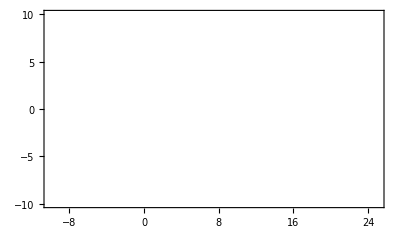

```mathematica
Show[ContourPlot[phi[x,y,t],{x,-10,25},{y,-10,10},
Contours->Table[k,{k,-100,1,100}], PlotPoints->40, AspectRatio->Automatic, ContourLabels->True],
Graphics[{Red, Disk[{s[t],0},0.4]}]]
```

```mathematica
ss2=
Table[Show[Plot3D[phi[x,y,t],{x,-10,25},{y,-10,10}]], {t,0,30,0.25}];
Export["D://lienard-wiechert-plot3d.gif",ss2]
```

D://lienard-wiechert-plot3d.gif

```mathematica
ss3=
Table[Plot3D[phi[x,y,t],{x,-10,25},{y,-10,10}], {t,0,50,2}];
Export["D://lienard-wiechert-plot3d3.gif",ss3]
```

D://lienard-wiechert-plot3d3.gif

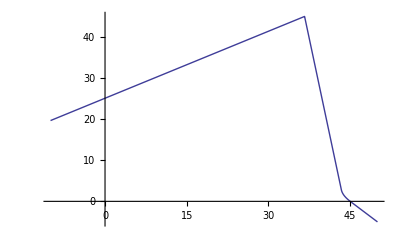

```mathematica
t=45;Plot[phi[x,0,t],{x,-10,50}]
```

```mathematica
Value[phi[x,0,t],{x,-10,50}]
```

Value[41.4,{30,-10,50}]